# FAQ: “Sessie” Introduction

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

The toy “universe” is a string of characters, whose initial state can have any length and can contain any characters. (Two infinities here: length of string and size of the alphabet from which the characters are taken.) The “laws of nature” for the SSS are codified by a ruleset: a set of replacement instructions, each giving a string to search for and the string to replace it with. Ex: {“AB”->”BA”}. (More infinities: there is no limit on the number of rules in the ruleset, nor on the size of the strings, nor on the characters in the strings.)

In a sequential substitution system, rules must be applied sequentially in order (use the first rule if possible, the second only if the first fails, etc.) from left-to-right: if the first usable rule can be used at multiple locations in the state string, we apply it in the first possible (left-most) position.

Each application of any rule is an event, and each event destroys and/or creates cells (or letters) in the state string.  Two events are considered to be causally connected if a cell created by one is destroyed by the other. (Later we’ll explain more about how the causal network connections work, i.e. the lines that connect the nodes.)

The causal network of an SSS can be visualized by treating all events as graph nodes and the causal connections between them as graph edges.

The basic command to display a Sessie is SSS. The template for usage is:

SSS[ruleset, initial state, number of steps, options]

Ex:



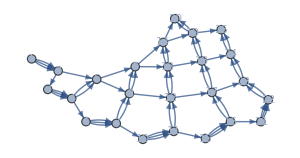
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss1 = SSS[{"ABA"->"AAB","A"->"ABA"},"AB",25, RulePlacement->Left, SSSSize -> 100, NetSize -> 300];
```

Try changing the rules in the ruleset, or the initial state string, or the number of steps.  Or try it with some options:

```mathematica
sss2 = SSS[{"ABA"->"AAB","A"->"ABA"},"ABCD",500,SSSMax->40,SSSSize->100,NetSize->450,VertexLabels->None];
```

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

To find more information on any function use a question mark. For example:

```mathematica
?SSS
```

Once the sessie has been created you can display it, change options, look at the network, etc. Choose options using SSSInteractiveDisplay, click one of the use buttons for one time or default use.

```mathematica
SSSInteractiveDisplay[sss2]
```

We might chose the GraphPlot3D display for the network. (Clicking and dragging with the mouse shows different view points.)

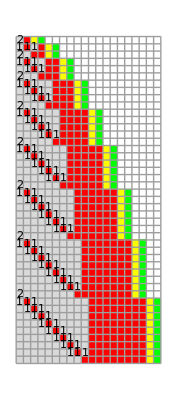
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics3D-

```mathematica
SSSDisplay[sss2,Min->1,Max->500,SSSMin->Automatic,SSSMax->45,NetMin->Automatic,NetMax->224,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot3D},ImageSize->170.,NetSize-> 350,SSSSize->{Automatic,220},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False]
```

SSSAnimate shows the order the network is created.

```mathematica
SSSAnimate[sss1]
```

Other components of the Sessie object can also be studied individually.

```mathematica
sss1[["RuleSet"]]
```

{ABA→AAB,A→ABA}

```mathematica
sss1[["Evolution"]]
```

{AB,ABAB,AABB,ABAABB,AABABB,AAABBB,ABAAABBB,AABAABBB,AAABABBB,AAAABBBB,ABAAAABBBB,AABAAABBBB,AAABAABBBB,AAAABABBBB,AAAAABBBBB,ABAAAAABBBBB,AABAAAABBBBB,AAABAAABBBBB,AAAABAABBBBB,AAAAABABBBBB,AAAAAABBBBBB,ABAAAAAABBBBBB,AABAAAAABBBBBB,AAABAAAABBBBBB,AAAABAAABBBBBB,AAAAABAABBBBBB}

```mathematica
sss1[["RulesUsed"]]
```

{2,1,2,1,1,2,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1}

The RuleSet contains the “laws of nature” for this toy universe which are always invoked sequentially. The first rule is always used before the second, if possible, and the rule is always used in the left most position in the state string. The Evolution gives the list of all state strings from the initial state on.  For instance, sss1 only contains the first 25 time steps. The colored box picture is a visual representation of these state strings. The component RulesUsed gives the list of which rules were used at each time step.